## Recovering Figure for Eigenvalue spectra

```mathematica
returncomplexplot[oncompartments_]:=Module[{memorysize=oncompartments},
newscheme={RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[0.915, 0.3325, 0.2125]};
eigenvals={};
For[leach=0.25,leach≤1.75,leach=leach+0.5,
Table[Subscript[b, i]=1,{i,0,memorysize}];
Table[Subscript[d, i]=0.98,{i,0,memorysize}];
μ=0.1;
ϵ=leach;
diagelements=Table[Subscript[b, i]-Subscript[d, i]-ϵ,{i,memorysize,1,-1}];
PrependTo[diagelements,Subscript[b, 0]-Subscript[d, 0]-μ];
A=Normal[SparseArray[{Band[{1,memorysize+1}]->ϵ,Band[{1,1}]->diagelements,Band[{2,1}]->Table[If[i==1,μ,ϵ],{i,memorysize}]},{memorysize+1,memorysize+1}]];
sorted=ReverseSortBy[Eigensystem[A]//Transpose,First];
AppendTo[eigenvals,sorted⟦All,1⟧]];
{m1,m2,m3,m4}=Graphics/@{Circle[{0,0},1],Disk[{0,0},1],Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}],Polygon[{{-0.5,-0.5},{0.5,-0.5},{0,√3/4}}]};
ComplexListPlot[eigenvals,Frame->True,Joined->{False,False,False,False},PlotMarkers->{Automatic,Medium},PlotStyle->newscheme,FrameStyle->Directive[Black,Thickness[0.003]],PlotTheme->"Scientific",FrameLabel->{Style["Real Part",18],Style["Imaginary Part",18]},AspectRatio->1,AxesOrigin->{0,0},ImageSize->Medium,PlotRange->{{-4,1},{-2,2}}]]
```

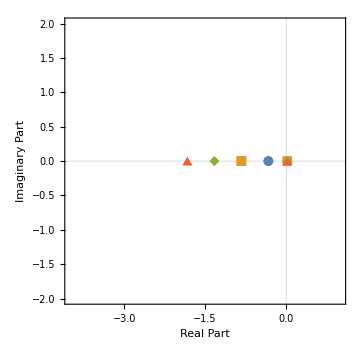
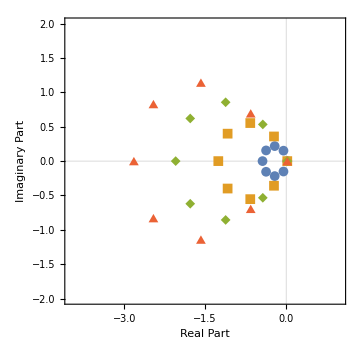
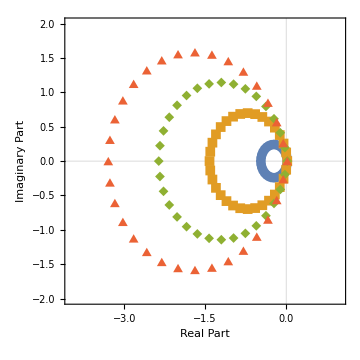

```mathematica
Table[returncomplexplot[n],{n,{1,7,31}}]
```